```mathematica
V[r_]=-(1/r)-(1.0415223038416566 E^(-0.9990999998788636 r))/r;α=2.;
```

```mathematica
radialeq=V[r] f[r]-1/α f''[r];
radialξ=Simplify[radialeq/.f->(ψ[ArcTan[#]]&)/.r->Tan[ξ],0<ξ<π/2];
```

```mathematica
Module[{shift=10,n=20,ev,evShifted},{ev,ef}=NDEigensystem[{shift ψ[ξ]+radialξ(*+NeumannValue[0,r==d]*),DirichletCondition[ψ[ξ]==0,True]},ψ,{ξ,0,π/2},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.00001}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift]
```

{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.00129369}

```mathematica
amplitude=Table[NIntegrate[(ef[[i]][ArcTan[r]])^2,{r,0,∞}],{i,5}]^(-1/2)
```

{0.805043,0.313619,0.15642,0.0975397,0.0681013}

```mathematica
NIntegrate[(Laplacian[amplitude[[#]]  ef[[#]][ArcTan[r]],{r}]^2),{r,0,∞}]&/@{1,2,3,4,5}
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.0689113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 75.0657 和 0.00101032.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.0689113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 5.8981 和 0.0000584906.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {r} = {0.0689113} 处的 r 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.38389 和 0.0000151595.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

{75.0657,5.8981,1.38389,0.533537,0.259684}

```mathematica
NIntegrate[((amplitude⟦4⟧ ef⟦4⟧[ArcTan[r]]){r})^2,{r,0,2000},WorkingPrecision->20]
```

NIntegrate::precw: 参数函数的精度 ((-(0.195079 r InterpolatingFunction[«1»][ArcTan[r]])/((1+r^2)^2)+(0.0975397 «1»)/((1+r^2)^2))^2) 小于 WorkingPrecision (20.).

NIntegrate::inumr: 在以 {{0,2000}} 为界的区域内，对于所有采样点，计算被积函数 (-(0.1950793517663529375 r InterpolatingFunction[«1»][ArcTan[r]])/((1+r^2)^2)+(0.097539675883176468751 «1»)/((1+r^2)^2))^2 得到非数值.

NIntegrate[((amplitude⟦4⟧ ef⟦4⟧[ArcTan[r]]){r})^2,{r,0,2000},WorkingPrecision→20]

```mathematica
ef⟦4⟧[ArcTan[r]]
```

InterpolatingFunction[{{0., 1.5708}}, <>][ArcTan[r]]

```mathematica
NIntegrate[(Laplacian[amplitude[[#]] ef[[#]][ArcTan[r]],{r}]^2),{r,0,∞}]&[6]
```

Part::partw: {0.805043,0.313619,0.156419,0.0975397,0.0681013} 的部分 6 不存在.

NIntegrate::inumr: 在以 {{∞,0.}} 为界的区域内，对于所有采样点，计算被积函数 (-(«1»)/((1+r^2)^2)+(«1»)/((1+r^2)^2))^2 得到非数值.

NIntegrate[((amplitude⟦6⟧ ef⟦6⟧[ArcTan[r]]){r})^2,{r,0,∞}]

```mathematica
NIntegrate[ef[[6]][ArcTan[r]]^2,{r,0,∞},MaxRecursion->50]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;a=1;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]
Vs2[r_]=- α/r Erf[r/(√2 a)]+c2 a^2 δa[r]+d1 a^4 Laplacian[δa[r],{r,θ,ϕ},"Spherical"]/.{c2->-53.12727,d1->-6.00285}
```

(c1 ⅇ^(-r^2/2))/(2 √2 π^(3/2))-Erf[r/(√2)]/r

-3.37324 ⅇ^(-r^2/2)-6.00285 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r

```mathematica
Module[{shift=10,n=20,ev,evShifted},{ev,efVs2}=NDEigensystem[{shift f[r]+Vs2[r] f[r]-1/2 f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f,{r,0,2000},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift]
```

{-1.33573,-0.188775,-0.071308,-0.0374575,-0.0230657,-0.0156238,-0.0112801,-0.00852543,-0.00666937,-0.0053596,-0.00440097,-0.00367832,-0.00312009,-0.00267993,-0.00232675,-0.00203906,-0.0018016,-0.00160333,-0.00143608,-0.00129369}

```mathematica
(*ψ(0)*)
```

```mathematica
amplitude[[#]]  ef[[#]][ArcTan[0]]&/@{1,2,3,4,5}
```

{0.,0.,0.,0.,0.}

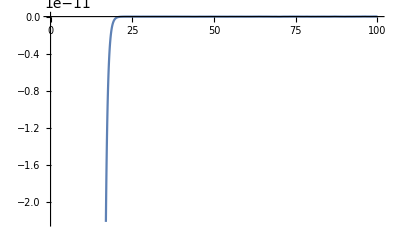
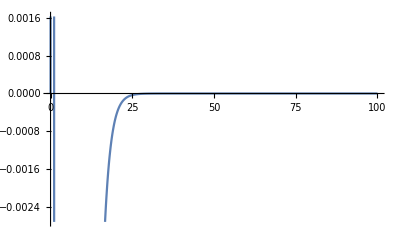
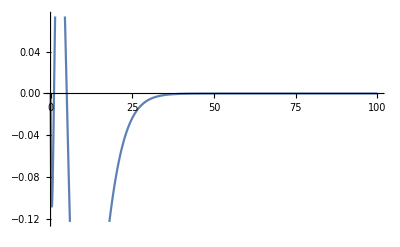
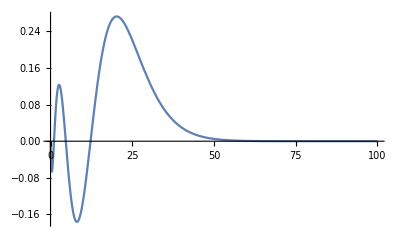
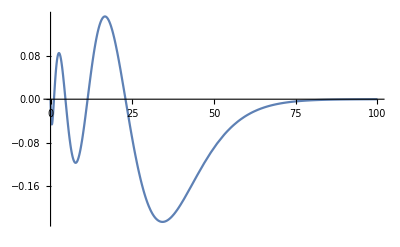

```mathematica
Plot[amplitude[[#]]  ef[[#]][ArcTan[r]],{r,0,100}]&/@{1,2,3,4,5}
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
NLimit[amplitude[[#]]  ef[[#]][ArcTan[r]],r->0]&/@{1,2,3,4,5}
```

{2.19578×10^-7,-2.92357×10^-7,1.48208×10^-7,9.29632×10^-8,6.50749×10^-8}

```mathematica
NLimit[(amplitude[[#]]  ef[[#]][ArcTan[r]])/r,r->0]&/@{1,2,3,4,5}
```

```mathematica
{-5.491933621585851,1.3917260094491244,-0.6629026822638356,-0.4088083126209399,-0.28414785818335714}/√(4π)
```

{-1.54925,0.392599,-0.187001,-0.115323,-0.0801566}

```mathematica
{1.5,0.383,0.1837,0.11353,0.079005}/0.079005
```

{18.9861,4.84779,2.32517,1.437,1.}